```mathematica
n=1000; m=10000;
```

```mathematica
(*Este código debería calcular el número de ccs, el tamaño de las mismas, la distribución de grados, el GCC, el MCC y la Asortatividad*)kaux={}; cc={}; ncc=0; scc={}; x=0; lncc={}; lvd={}; lscc={}; lgc={}; lmc={}; llcc={}; Do[kaux={}; v={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\Alfa075Test.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\Alfa075Test.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}],cc=ConnectedComponents[Graph[t]],  x=Evaluate[n-Total[Table[Length[cc[[i]]], {i, 1, Length[cc]}]]],Do[{ cc=Join[cc, {1}]}, x], lscc=Join[lscc, Table[Length[cc[[i]]], {i, 1, Length[cc]}]]},m];
```

```mathematica
kaux={}; cc={}; ncc=0; scc={}; x=0; lncc={}; lvd={}; lscc={}; lgc={}; lmc={}; llcc={}; Do[{kaux={}; v={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\Alfa075Test.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\Alfa075Test.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}],cc=ConnectedComponents[Graph[t]],  x=Evaluate[n-Total[Table[Length[cc[[i]]], {i, 1, Length[cc]}]]],Do[{ cc=Join[cc, {1}]}, x], lscc=Join[lscc, Table[Length[cc[[i]]], {i, 1, Length[cc]}]]},m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
blncc=HistogramList[lncc]; hlncc=Table[{Floor[(blncc[[1,i]]+blncc[[1, i+1]])/2], blncc[[2, i]]/(Length[lncc]*(blncc[[1,2]]-blncc[[1,1]]))}, {i, 1, Length[blncc[[2]]]}];TableForm[N[hlncc]]
```

```mathematica
N[MeanDeviation[lncc]]
```

7.07549

```mathematica
w=(Max[lscc]-Min[lscc])/Sqrt[Length[lscc]]; blscc=HistogramList[lscc, {Min[lscc], Max[lscc], w}]; hlscc=Table[{Floor[blscc[[1, i]]], blscc[[2, i]]/(Length[lscc]*w)}, {i, 1, Length[blscc[[2]]]}];TableForm[N[hlscc]]
```

```mathematica
blvd=HistogramList[lvd]; hlvd=Table[{Floor[(blvd[[1,i]]+blvd[[1, i+1]])/2], blvd[[2, i]]/(Length[lvd]*(blvd[[1,2]]-blvd[[1,1]]))}, {i, 1, Length[blvd[[2]]]}];TableForm[N[hlvd]]
```

```mathematica
N[Mean[lvd]]
```

2.98934

```mathematica
N[MeanDeviation[lgc]]
```

0.0131241

```mathematica
w=(Max[llcc]-Min[llcc])/Sqrt[Length[llcc]]; bllcc=HistogramList[llcc, {Min[llcc], Max[llcc], w}]; hllcc=Table[{bllcc[[1, i]], bllcc[[2, i]]/(Length[llcc]*w)}, {i, 1, Length[bllcc[[2]]]}];TableForm[N[hllcc]]
```

```mathematica
MeanClusteringCoefficient[{1<-> 2}]
```

0

```mathematica
t={3<->4, 5<->6, 7<->8, 1<->3};
```

```mathematica
r=t;
```

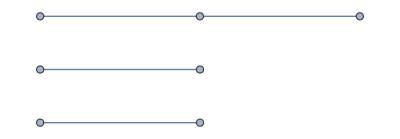

```mathematica
Graph[r]
```

```mathematica
kaux={}; cc={}; ncct=0; nccr=0; scct={}; sccr={}; x=0; lncct={};lnccr={}; lvd={}; lscct={};lsccr={};  Do[{kaux={}; v={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\NetN3000.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\NetN3000.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n], v=VertexDegree[Graph[t]],cct=ConnectedComponents[Graph[t]],ccr=ConnectedComponents[Graph[r]],  x=Evaluate[n-Total[Table[Length[cct[[i]]], {i, 1, Length[cct]}]]],Do[{ cct=Join[cct, {1}], ccr=Join[ccr, {1}],v=Join[v, {0}]}, x], ncct=Length[cct], nccr=Length[ccr],lscct=Join[lscct, Table[Length[cct[[i]]], {i, 1, Length[cct]}]], lsccr=Join[lsccr, Table[Length[ccr[[i]]], {i, 1, Length[ccr]}]], lvd=Join[lvd, v],  lncct=Join[lncct, {ncct}] , lnccr=Join[lnccr, {nccr}]},m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
kaux={}; cc={}; ncct=0; nccr=0;  x=0; lncct={};lnccr={}; lvd={};  Do[{kaux={}; v={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_090.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_090.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n], v=VertexDegree[Graph[t]],cct=ConnectedComponents[Graph[t]],ccr=ConnectedComponents[Graph[r]],  x=Evaluate[n-Total[Table[Length[cct[[i]]], {i, 1, Length[cct]}]]],Do[{ cct=Join[cct, {1}], ccr=Join[ccr, {1}],v=Join[v, {0}]}, x], ncct=Length[cct], nccr=Length[ccr], lvd=Join[lvd, v],  lncct=Join[lncct, {ncct}] , lnccr=Join[lnccr, {nccr}]},m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
blncc=HistogramList[lncct]; hlncc=Table[{(blncc[[1,i]]+blncc[[1, i+1]])/(2*n), (blncc[[2, i]]*(2*n))/(Length[lncct]*(blncc[[1,2]]-blncc[[1,1]]))}, {i, 1, Length[blncc[[2]]]}];TableForm[N[hlncc]]
```

```mathematica
blncc=HistogramList[lnccr]; hlncc=Table[{(blncc[[1,i]]+blncc[[1, i+1]])/(2*n), (blncc[[2, i]]*(2*n))/(Length[lnccr]*(blncc[[1,2]]-blncc[[1,1]]))}, {i, 1, Length[blncc[[2]]]}];TableForm[N[hlncc]]
```

```mathematica
Print[N[Mean[lncct]]]; Print[N[MeanDeviation[lncct]]]; Print[N[Mean[lnccr]]]; Print[N[MeanDeviation[lnccr]]];
```

```mathematica
w=(Max[lscct]-Min[lscct])/(Sqrt[Length[lscct]]); blscc=HistogramList[lscct, {Min[lscct], Max[lscct], w}]; hlscc=Table[{Floor[blscc[[1, i]]]/n, (blscc[[2, i]]*n)/(Length[lscct]*w)}, {i, 1, Length[blscc[[2]]]}];TableForm[N[hlscc]]
```

```mathematica
w=(Max[lsccr]-Min[lsccr])/(Sqrt[Length[lsccr]]); blscc=HistogramList[lsccr, {Min[lsccr], Max[lsccr], w}]; hlscc=Table[{Floor[blscc[[1, i]]]/n, (blscc[[2, i]]*n)/(Length[lsccr]*w)}, {i, 1, Length[blscc[[2]]]}];TableForm[N[hlscc]]
```

```mathematica
blvd=HistogramList[lvd]; hlvd=Table[{Floor[(blvd[[1,i]]+blvd[[1, i+1]])/2], blvd[[2, i]]/(Length[lvd])}, {i, 1, Length[blvd[[2]]]}];TableForm[N[hlvd]]
```

```mathematica
Print[N[Mean[lvd]]]; Print[N[StandardDeviation[lvd]]]
```

2.98915

1.33572

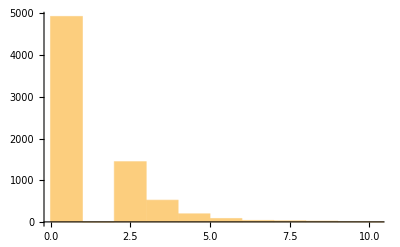

```mathematica
Histogram[lsccr]
```

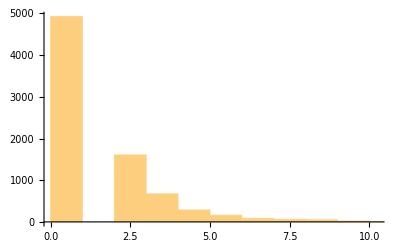

```mathematica
Histogram[lscct]
```

```mathematica
N[GlobalClusteringCoefficient[Graph[r]]]
```

0.418195

```mathematica
N[GlobalClusteringCoefficient[Graph[t]]]
```

0.428773

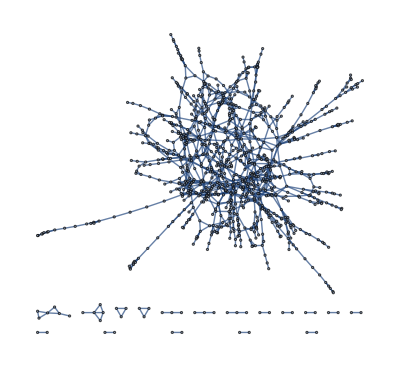

```mathematica
Graph[t]
```

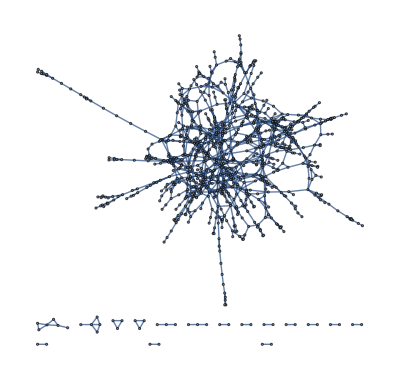

```mathematica
Graph[r]
```

```mathematica
Mean[VertexDegree[r]]
```

1458/475

```mathematica
Mean[VertexDegree[t]]
```

1458/475

```mathematica
n=1000; m=10000;
```

```mathematica
kaux={}; cc={}; ncct=0; nccr=0;  x=0; lncct=ConstantArray[0, n];vertex=ConstantArray[0, n];lnccr=ConstantArray[0, n];   Do[{kaux={}; v={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_015.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_015.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n], v=VertexDegree[Graph[t]],cct=ConnectedComponents[Graph[t]],ccr=ConnectedComponents[Graph[r]],  x=Evaluate[n-Total[Table[Length[cct[[i]]], {i, 1, Length[cct]}]]],Do[{ cct=Join[cct, {1}], ccr=Join[ccr, {1}],v=Join[v, {0}]}, x], ncct=Length[cct], nccr=Length[ccr], Do[{vertex[[i]]=vertex[[i]]+Count[v, i-1]}, {i, 1, n}], lncct[[ncct]]=lncct[[ncct]]+1, lnccr[[nccr]]=lnccr[[nccr]]+1},m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
T=Total[vertex]; M=N[Sum[{(i-1)*vertex[[i]]}, {i, 1, n}]/T];Print[M];SD=N[Sqrt[Sum[vertex[[i]]*(i-M-1)^2, {i, 1, n}]/(T-1)]]; Print[SD];
```

{2.27705}

{0.901737}

```mathematica
Total[vertex]
```

100000

```mathematica
T=Total[lncct]; M=N[Sum[{i*lncct[[i]]}, {i, 1, n}]/T];Print[M];SD=N[Sqrt[Sum[lncct[[i]]*(i-M)^2, {i, 1, n}]/(T-1)]]; Print[SD];
```

{36.0527}

{4.88699}

```mathematica
T=Total[lnccr]; M=N[Sum[{i*lnccr[[i]]}, {i, 1, n}]/T];Print[M];SD=N[Sqrt[Sum[lnccr[[i]]*(i-M)^2, {i, 1, n}]/(T-1)]]; Print[SD];
```

{23.9631}

{4.39685}

```mathematica
n=500; m=1000;
```

```mathematica
kaux={}; cc={}; ncct=0; nccr=0;  x=0; lncct=ConstantArray[0,300];lnccr=ConstantArray[0, 300];   Do[{kaux={}; v={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\NetN3000.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\NetN3000.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n],cct=ConnectedComponents[Graph[t]],ccr=ConnectedComponents[Graph[r]],  x=Evaluate[n-Total[Table[Length[cct[[i]]], {i, 1, Length[cct]}]]],Do[{ cct=Join[cct, {1}], ccr=Join[ccr, {1}]}, x], ncct=Length[cct], nccr=Length[ccr], lncct[[ncct]]=lncct[[ncct]]+1, lnccr[[nccr]]=lnccr[[nccr]]+1},m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
T=Total[lncct]; M=N[Sum[{i*lncct[[i]]}, {i, 1, Length[lncct]}]/T];Print[N[M/n]];SD=N[Sqrt[Sum[lncct[[i]]*(i-M)^2, {i, 1,Length[lncct]}]/(T-1)]]; Print[N[SD/n]];
```

{0.078994}

{0.00503335}

```mathematica
.
```

```mathematica
T=Total[lnccr]; M=N[Sum[{i*lnccr[[i]]}, {i, 1, Length[lnccr]}]/T];Print[N[M/n]];SD=N[Sqrt[Sum[lnccr[[i]]*(i-M)^2, {i, 1, Length[lnccr]}]/(T-1)]]; Print[N[SD/n]];
```

{0.0580529}

{0.0042124}

```mathematica
(*Degree distribution*)
```

```mathematica
n=1000; m=10000; string="D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre_6_-_Maestria_1\\Trabajo Especial\\Net_Generation\\n0667.txt";
kaux={}; cc={}; ncct=0; nccr=0;  x=0; kdistr=ConstantArray[0, {100}] ;  Do[{kaux={}; spression=ToExpression[StringSplit[ReadLine[string]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine[string]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], vd=VertexDegree[t], For[i=1, i<Length[kdistr], i++, {kdistr[[i+1]]+=Count[vd, i]}], kdistr[[1]]=2*n-Length[vd]},m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Normalization*)
kdistr=kdistr/Total[kdistr];
(*TableExport*)
TableForm[N[kdistr]]
```

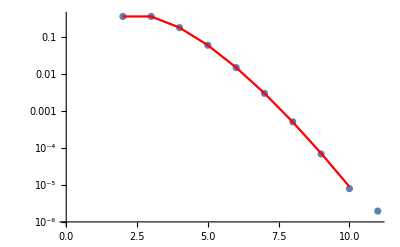

```mathematica
Show[ListPlot[kdistr, ScalingFunctions->"Log"], ListPlot[Table[Exp[-1]/Gamma[i-1], {i, 1, 10}], PlotStyle->Red, ScalingFunctions->"Log", Joined->True]]
```

```mathematica
k=N[Sum[(i-1)*kdistr[[i]], {i,1,Length[kdistr]}]]
```

3.9957

```mathematica
σ=N[Sum[(i-1-3.99570446486374)^2*kdistr[[i]], {i,1,Length[kdistr]}]]
```

2.99561

```mathematica
kdistr2=kdistr*10000*2000
```

{-20000000/10004807,10067420000000/10004807,29879100000000/10004807,44898210000000/10004807,44850200000000/10004807,33547150000000/10004807,20148900000000/10004807,10052490000000/10004807,4307920000000/10004807,1593810000000/10004807,538100000000/10004807,153340000000/10004807,45960000000/10004807,9490000000/10004807,3920000000/10004807,150000000/10004807,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
N[StandardDeviation[kdistr2]]/(10000*2000)
```

0.0397878

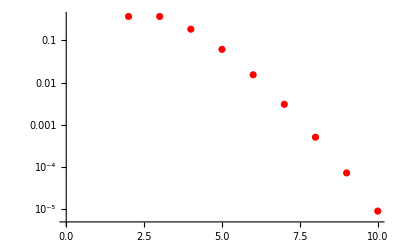

```mathematica
ListPlot[Table[Exp[-1]/Gamma[i-1], {i, 1, 10}], PlotStyle->Red, ScalingFunctions->"Log"]
```

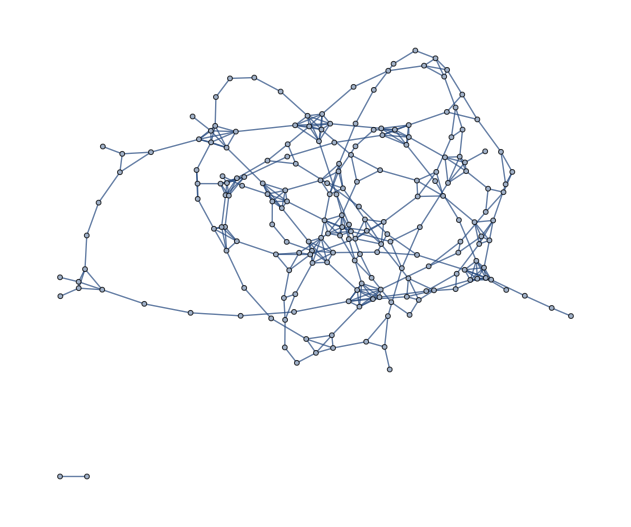

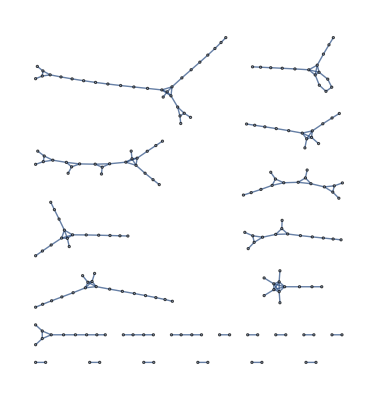

```mathematica
n=100; m=1; string="D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre_6_-_Maestria_1\\Trabajo Especial\\Net_Generation\\Test067.txt";
kaux={}; cc={}; ncct=0; nccr=0;  x=0; kdistr=ConstantArray[0, {100}] ;  Do[{kaux={}; spression=ToExpression[StringSplit[ReadLine[string]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine[string]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], vd=VertexDegree[t], For[i=1, i<Length[kdistr], i++, {kdistr[[i+1]]+=Count[vd, i]}], kdistr[[1]]=2*n-Length[vd]},m]; Graph[t]
```